## General Second-Order Runge-Kutta — Forced Oscillation

## Done in class, January 31, 2025

This is the fifth notebook for you to finish in-class.

### Forced Oscillation

#### Problem Description

```mathematica
omega=1.0;
externalForce[t_]:=100Sin[omega t]
springConstant = 20;
force[t_, x_, v_]:=-springConstant x-v+externalForce[t]
mass=5;
a[t_, x_, v_] := force[t, x,v]/mass;
tInitial = 0;
tFinal = 100; 
steps = 25000;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Conditions

Let’s let the spring be initially unstretched with no velocity and see what the external force does to it:

```mathematica
xInitial=0.0;
vInitial=0.0;
(* We also want to be able to visualize the external force, so let's tack it on. *)
initialConditions={tInitial,xInitial,vInitial, externalForce[xInitial]/springConstant};
```

#### General Second-Order Runge-Kutta — Implementation

The implementation will be almost the same as in the damped oscillation notebook you just completed. What small things have to be changed?

```mathematica
alpha=1;
rungeKutta2[cc_]:=(
(* Extract time, position, and velocity from the list. *)
curTime=cc[[1]];
curPosition = cc[[2]];
curVelocity=cc[[3]];
(* Implement the six equations in the theory above. *)
tStar=curTime+alpha deltaT;
xStar=curPosition+curVelocity alpha deltaT;
vStar=curVelocity+a[curTime, curPosition, curVelocity]alpha deltaT;
newTime=curTime+deltaT;
newVelocity=curVelocity+((1-1/(2alpha))a[curTime, curPosition,curVelocity]+1/(2alpha)a[tStar, xStar,vStar])deltaT;
newPosition=curPosition+(curVelocity+newVelocity)deltaT/2;
(* We also want to be able to visualize the external force, so let's tabulate it. *)
{newTime, newPosition, newVelocity, externalForce[newTime]/springConstant}
)
```

#### Displaying Forced Oscillation

Nest the procedure and then transpose the results to produce position and velocity plots:

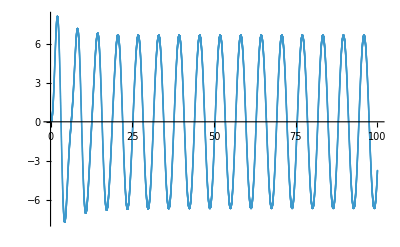

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
positionPlot = ListPlot[Transpose[rk2ResultsTransposed[[{1,2}]]]]
```

```mathematica
positions=rk2ResultsTransposed[[2]];
forces=rk2ResultsTransposed[[4]];
```

```mathematica
Animate[NumberLinePlot[{positions[[step]], forces[[step]]},PlotRange->{-25,25}],{step, 0, steps, 1}]
```

#### Conclusion / Commentary

Our oscillator now has the force law F(x)=-20x-v and in addition a sinusoidal external force.

This thing is pretty interesting to play around with. Once everybody has it working, we will start understanding what is being animated.